# Numerical solution to Meissner' s two dimensial problem : the Reulaux triangle.

Meissner' s problem asks for the convex body of  unit width and minimal volume. In two dimensions the solution is known explicitly, as the Reulaux triangle.

200

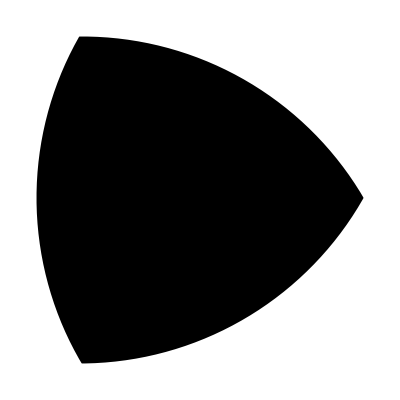
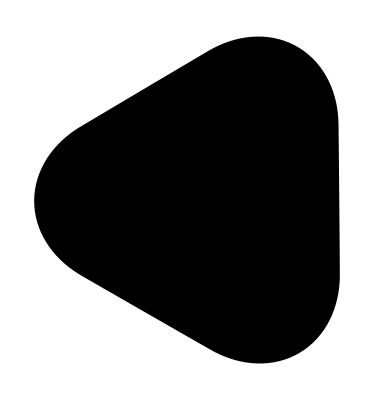

```mathematica
Module[{data=ImportFromTxt[MinkowskiBinDirectory<>"/Meissner_2.txt"],x,pts,scaledPts,dualPts,n},
x="x"/.data;
x=Join[x,1-x];
n=Length@x;
pts={"N::StdFromEigen(NV(pts.row(0)))"/.data,"N::StdFromEigen(NV(pts.row(1)))"/.data};
pts=Transpose@pts;
scaledPts=MapThread[#1/#2&,{pts,x}];

dualPts=Table[Inverse[scaledPts[[{i,Mod[i,n]+1}]] ].{1,1},{i,n}];

Print[Length[pts]];
{Graphics[Polygon[dualPts]],Graphics[Polygon[scaledPts]]}
]
```

```mathematica
(*True volume of Meissner solid*)
(Pi-Sqrt[3])/2.
```

0.704771